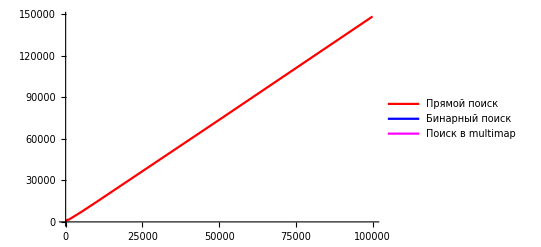

```mathematica
straightSort = ListLinePlot[{{100, 255}, {500, 1468}, {1000, 1591}, {5000, 7033}, {10000, 14290}, {50000, 73570}, {100000, 148161}}, ColorFunction->Function[{}, Red], PlotLegends->LineLegend[{Red,Blue, Magenta},{"Прямой поиск","Бинарный поиск", "Поиск в multimap"}], PlotRange->{{0, 100000}, All}]
```

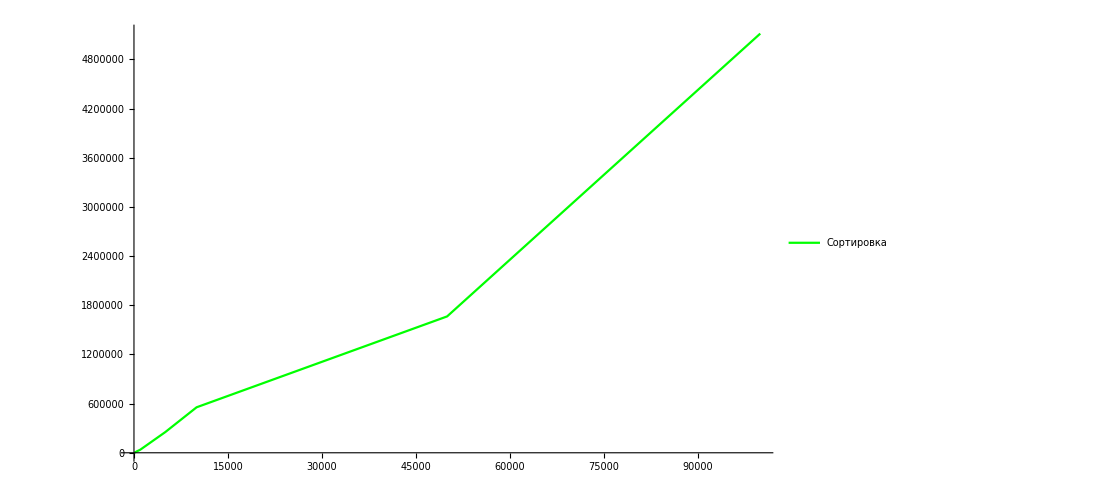

```mathematica
sort = ListLinePlot[{{100, 2672}, {500, 18684}, {1000, 37075}, {5000, 252430}, {10000, 554972}, {50000, 1663731}, {100000, 5114542}}, ColorFunction->Function[{}, Green], PlotLegends->LineLegend[{Green},{"Сортировка"}]]
```

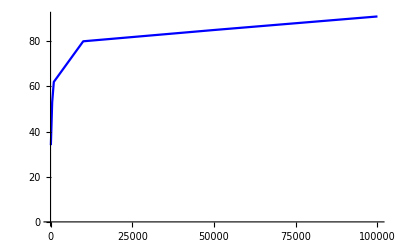

```mathematica
binarySearch = ListLinePlot[{{100, 34}, {500, 53}, {1000, 62}, {5000, 70}, {10000, 80}, {50000, 85}, {100000, 91}},PlotRange->{{0, 100000}, All}, ColorFunction->Function[{}, Blue]]
```

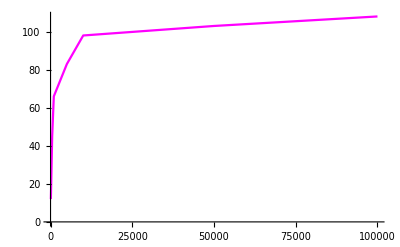

```mathematica
multimapSearch = ListLinePlot[{{100, 12}, {500, 45}, {1000, 66}, {5000, 83}, {10000, 98}, {50000,103}, {100000, 108}}, ColorFunction->Function[{}, Magenta]]
```

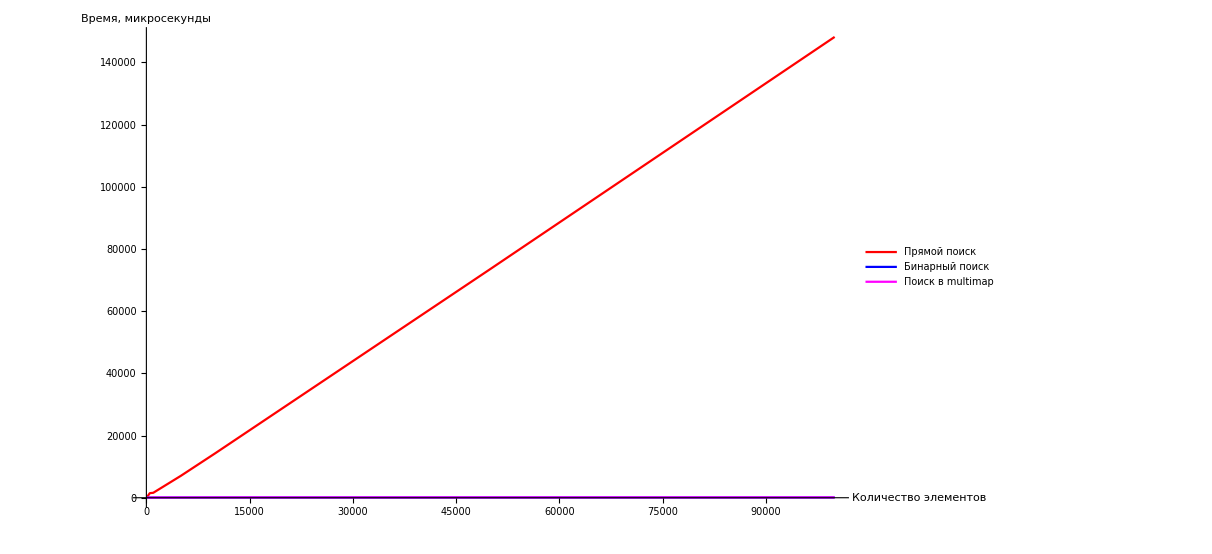

```mathematica
Show[straightSort,  binarySearch, multimapSearch, PlotRange->Automatic, AxesLabel->{"Количество элементов", "Время, микросекунды"}]
```